/Volumes/Macintosh HD/Users/peterweilnbock/Documents/UNI/Masterarbeit

-Graphics-

1.09585×10^30

System defined

NDSolve::ndsz: At r == 1.20023×10^6, step size is effectively zero; singularity or stiff system suspected.

{{m→                             -6            6
InterpolatingFunction[{{1. 10  , 1.20023 10 }}, <>],d→                             -6            6
InterpolatingFunction[{{1. 10  , 1.20023 10 }}, <>]}}

-Graphics-

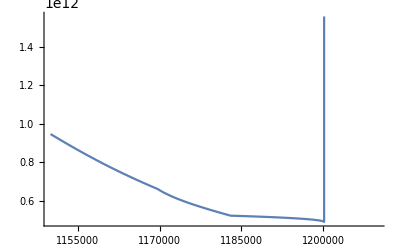

-Graphics-

Radius=rMax

Density at R=100 000={6.31783×10^12}

Preassure at R=100 000={6.57371×10^30}

Mass={                             -6            6
InterpolatingFunction[{{1. 10  , 1.20023 10 }}, <>][rMax]}

Stopping ρ=2.×10^8

```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
AppendTo[$Path,"//users//peterweilnboeck//mathematica//"];
Get["CustomTicks`"]
G:=6.67420000000000000000000000000000000000000000000000000000000000*10^(-8);
c:=2.99792458000000000000000000000000000000000000000000000000000000*10^(10);
(*G:=1;
c:=1;*)
γ:=2.75;
K:=1.982*10^(-6);
ρc:=2.0*10^14
(*ρc:=5.0*10^(14);*)
(*γ:=0.3;
K:=1;
ρc:=1;*)
(*pc:=K*ρc^(γ);*)
r0:=10^(-6);
rSwitch:=10^(-8);

ρ[r_]=d[r];
SetDirectory[NotebookDirectory[]]
points:=Import["EOS-numbers1.csv"]
k:=Interpolation[points];
Plot[k[x],{x,0,2*10^4}]
k[10^12]
p[r_]=k[d[r]];
pc:=p[ρc];
(*p[r_]=K*(d[r])^(γ);*)
(*ϵ[r_]=p[r]/((γ-1)ρ[r])*)
ϵ[r_]=0;

eqnM:={m'[r]==4 π r^2 ρ[r](1+ϵ[r]/(c^2))};
condM:={m[r0]==0};

eqnP:={-p'[r]==Piecewise[{{G*(ρ[r]*(1+ϵ[r]/(c^2))+p[r]/(c^2))*(4 π* r*p[r]/(c^2)),r≤rSwitch},{G*(ρ[r]*(1+ϵ[r]/(c^2))+p[r]/(c^2))*(m[r]+4 π* r^3 *p[r]/(c^2))/(r^2*(1-2 *G* m[r]/(r*c^2))),r>rSwitch}}]};
(*eqnP2:={-p'[r]==G*(ρ[r]*(1+ϵ[r]/(c^2))+p[r]/(c^2))*(4 π* r*p[r]/(c^2))};
eqnPReplace:={G*(ρ[r]*(1+ϵ[r]/(c^2))+p[r]/(c^2))*(4 π* r*p[r]/(c^2))}*)
condP:={p[r0]==pc};
condρ:={ρ[r0]==ρc};
stopCond:={WhenEvent[Evaluate[Re[d[r]]≤7.9],{rMax=r,"StopIntegration"}]}

system:=Join[eqnM,eqnP,condM,condρ,stopCond];
Print["System defined"];
sol = NDSolve[system, {m,d}, {r, r0, ∞},Method->{"StiffnessSwitching"}]

Plot[Evaluate[m[r]/.sol],{r,r0,10000000},PlotRange->All]
Plot[Evaluate[d[r]/.sol],{r,1150000,1210000},PlotRange->Automatic ]
Plot[Evaluate[p[r]/.sol],{r,1150000,1210000},PlotRange->All]
Print["Radius=",rMax,""];
Print["Density at R=100 000=",Evaluate[d[1000000]/.sol],""];
Print["Preassure at R=100 000=",Evaluate[p[1000000]/.sol],""];
Print["Mass=",Evaluate[m[rMax]/.sol],""];
Print["Stopping ρ=",ρc/1000000,""];

(*Last@Transpose[(m[5.0*10^(14)]/.sol)]
(m[5.0*10^(14)]/.sol)["Domain"]
Evaluate[m[5.0*10^(14)][(m[5.0*10^(14)]/.sol)["Domain"][[1,2]]]/.sol]
Plot[(m[10^α]/.sol)["Domain"][[1,2]],{α,6,16}]
Plot[Evaluate[m[10^α][(m[10^α]/.sol)["Domain"][[1,2]]]/.sol],{α,6,16}]*)
```

```mathematica
k[2.70879292920589*^13]
```

5.32646×10^31